```mathematica
Clear["Global`*"]
```

Mathematical models with case studies. p.31. 
Non-dimensional model! The replacement was x = x_sc x*, where x_sc = k1/i and t = t_sc t*, with t_sc = k1.

Data:

```mathematica
mdl = {deqn=x'[t]== 1- x[t], iv = x[0]==0};
$Assumptions=x>0&&t>0;
```

Solution:

Solve the IVP:

```mathematica
sln=DSolve[mdl,x[t],t]
```

{{x[t]→ⅇ^-t (-1+ⅇ^t)}}

Extract the solution:

```mathematica
x[t_]=x[t]/.sln[[1]]//FullSimplify
```

1-Cosh[t]+Sinh[t]

Verify that the solution satisfies the diff eqn and the initial condition:

```mathematica
deqn//FullSimplify
```

True

```mathematica
iv//FullSimplify
```

True

Find the max and min values of the solution:

```mathematica
FindMaximum[x[t],t]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{t→18.6498}}

```mathematica
FindMinimum[x[t],t]
```

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

FindMinimum::nrnum: The function value Overflow[] is not a real number at {t} = {-7.595×10^15}.

{-7.8646271519284410037349960327970786143`1.1288624837399295*^299860467688871,{t→-6.90454×10^14}}

Find limits:

```mathematica
Limit[x[t],t->0]
```

0

```mathematica
Limit[x[t],t->Infinity]
```

1

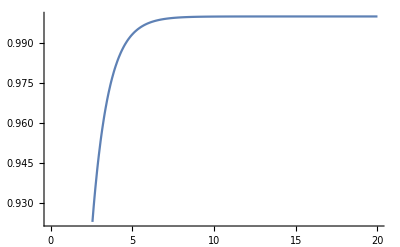

```mathematica
Plot[x[t],{t,0,20}]
```